```mathematica
SetDirectory[NotebookDirectory[]];
np=11;
Clear[data];
Clear[Data];
A=Import["array/A.dat","Table"];
K=Import["array/K.dat","Table"];
KA=K+A;
b={0,0,0,0,0,0,0,0,0,0,1};
d=-KA.b;
```

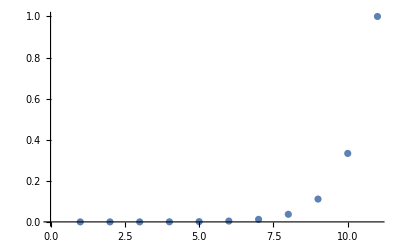

```mathematica
For[i=2,i<np,i++,
KA[[1,i]]=0;
KA[[i,1]]=0;
KA[[11,i]]=0;
KA[[i,11]]=0;
]
KA[[1,1]]=1;
KA[[11,11]]=1;
x=Inverse[KA].d;
x[[11]]=1.0;
x[[1]]=0;
ListPlot[x]
```